```mathematica
Clear["Global`*"]
```

# 1、Synaptic current pulse

```mathematica
(*定义输入电流*)
q=10;
τs=0.5;
tf=1;
Is=q*E^(-(t-tf)/τs)*UnitStep[t-tf];
figure1=Plot[Is,{t,0,10}, PlotRange->All,FrameLabel->{"时间t","电流I"},Frame->True];
```

```mathematica
(*定义无源膜*)
τm=5;
u=E^(-(t/τm))*UnitStep[t];
```

```mathematica
(*卷积*)
a=Convolve[u,Is,t,s];
figure2=Plot[a,{s,0,10},FrameLabel->{"时间t","电压u"},Frame->True];
```

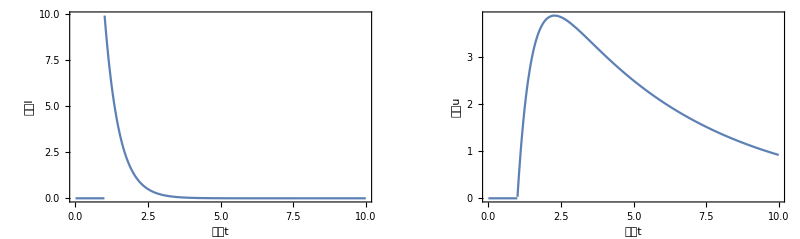

```mathematica
GraphicsGrid[{{figure1, figure2}}]
```